```mathematica
HH=Table[A[i][j],{i,4},{j,4}]
```

{{A[1][1],A[1][2],A[1][3],A[1][4]},{A[2][1],A[2][2],A[2][3],A[2][4]},{A[3][1],A[3][2],A[3][3],A[3][4]},{A[4][1],A[4][2],A[4][3],A[4][4]}}

```mathematica
For[i=1,i≤4,i++,For[j=1,j≤4,j++,A[i][j]=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]]];
```

```mathematica
MatrixForm[HH]
```

((0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)
(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0) | (0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0) | (0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)
(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)
(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1))

### Define Σij=σi@σj

```mathematica
For[i=0,i≤3,i++,For[j=0,j≤3,j++,Σ[i][j]=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]]];
```

### Define Hamiltonian with parameters

```mathematica
m=2.5;
t0=1;
t0'=1;
t0''=1;
t=1;
t'=1;
t''=1;
ϕ=1.05;
```

```mathematica
Ham[kx_,ky_,kz_]:=(m-t0 Cos[kx]-t0' Cos[ky]-t0'' Cos[kz])Σ[0][3]+t Sin[(kx-ϕ)/2](Sin[kx/2] Σ[1][1]+Cos[kx/2] Σ[2][1])+t' Sin[ky] Σ[0][2]+t'' Sin[kz]Σ[3][1]
```

```mathematica
MatrixForm[Ham[kx,ky,kz]]
```

(2.5-Cos[kx]-Cos[ky]-Cos[kz] | -ⅈ Sin[ky]+Sin[kz] | 0 | Sin[1/2 (-1.05+kx)] (-ⅈ Cos[kx/2]+Sin[kx/2])
ⅈ Sin[ky]+Sin[kz] | -2.5+Cos[kx]+Cos[ky]+Cos[kz] | Sin[1/2 (-1.05+kx)] (-ⅈ Cos[kx/2]+Sin[kx/2]) | 0
0 | Sin[1/2 (-1.05+kx)] (ⅈ Cos[kx/2]+Sin[kx/2]) | 2.5-Cos[kx]-Cos[ky]-Cos[kz] | -ⅈ Sin[ky]-Sin[kz]
Sin[1/2 (-1.05+kx)] (ⅈ Cos[kx/2]+Sin[kx/2]) | 0 | ⅈ Sin[ky]-Sin[kz] | -2.5+Cos[kx]+Cos[ky]+Cos[kz])

### Define dispersion function and plot

```mathematica
F[kx_,ky_,kz_]:=Sort[N[Eigenvalues[Ham[kx+0.0,ky+0.0,kz+0.0]]]];
```

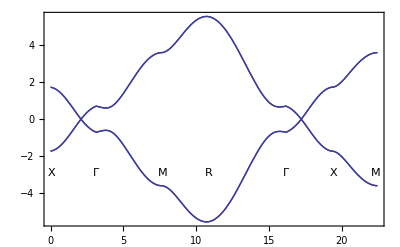

```mathematica
Plot[Piecewise[{{F[Pi-tt,0,0],tt≥0&&tt<Pi},{F[(tt-Pi)/Sqrt[2],(tt-Pi)/Sqrt[2],0],tt≥Pi&&tt<(1+Sqrt[2])Pi},{F[Pi,Pi,tt-(1+Sqrt[2])Pi],tt≥(Sqrt[2]+1)Pi&&tt<(Sqrt[2]+2)Pi},{F[Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3]],tt≥(2+Sqrt[2])Pi&&tt<(2+Sqrt[2]+Sqrt[3])Pi},{F[tt-(2+Sqrt[2]+Sqrt[3])Pi,0,0],tt≥(2+Sqrt[2]+Sqrt[3])Pi&&tt<(3+Sqrt[2]+Sqrt[3])Pi},{F[Pi,tt-(3+Sqrt[2]+Sqrt[3])Pi,0],tt≥(3+Sqrt[2]+Sqrt[3])Pi&&tt≤(4+Sqrt[2]+Sqrt[3])Pi}}],{tt,0,(4+Sqrt[2]+Sqrt[3])Pi},GridLines->{{{Pi,Dashed},{(1+Sqrt[2])Pi,Dashed},{(Sqrt[2]+2)Pi,Dashed},{(2+Sqrt[2]+Sqrt[3])Pi,Dashed},{(3+Sqrt[2]+Sqrt[3])Pi,Dashed},{(4+Sqrt[2]+Sqrt[3])Pi,Dashed}},{}},Epilog->{Inset["X",{0.05,0.08-3}],Inset["Γ",{Pi,0.08-3}],Inset["M",{(1+Sqrt[2])Pi+0.15,0.08-3}],Inset["R",{(2+Sqrt[2])Pi+0.15,0.08-3}],Inset["Γ",{(2+Sqrt[2]+Sqrt[3])Pi,0.08-3}],Inset["X",{(3+Sqrt[2]+Sqrt[3])Pi+0.15,0.08-3}],Inset["M",{(4+Sqrt[2]+Sqrt[3])Pi-0.15,0.08-3}]},Frame->True]
```

### Find the eigensystem and choose the two lower bands as VEC

```mathematica
ESYS[kx_,ky_,kz_]:=Eigensystem[Ham[kx,ky,kz]]
```

```mathematica
VEC[kx_,ky_,kz_]:=(Clear[VEC1,VEC2];For[i=1;j=1,i≤4,i++,If[ESYS[kx,ky,kz][[1]][[i]]<0,If[j==1,VEC1=ESYS[kx,ky,kz][[2]][[i]];j++,VEC2=ESYS[kx,ky,kz][[2]][[i]]]]];{VEC1,VEC2})
```

```mathematica
VEC[1,1,1]
```

{{-0.106982-0.383293 ⅈ,-0.426762+0.757228 ⅈ,-0.293438-0.00387742 ⅈ,0.},{0.140694-0.257539 ⅈ,0.,0.281388+0.281388 ⅈ,0.869207}}

### Build correlation function C[x,x’]

#### define numerical integral function

```mathematica
INT[y_,kx_,kz_,LL_,HL_,i_,j_]:=(Clear[int];
For[ii=LL;int=0,ii≤HL,ii=ii+0.1,int+=0.1y[kx,ii,kz,i,j]];int)
```

#### define the Core of Correlation function for integral

```mathematica
CORE[kx_,ky_,kz_,i_,j_]:=Exp[I (i-j) ky](KroneckerProduct[Conjugate[VEC[kx,ky,kz][[1]]],VEC[kx,ky,kz][[1]]]+KroneckerProduct[Conjugate[VEC[kx,ky,kz][[2]]],VEC[kx,ky,kz][[2]]])
```

#### define the Correlation function matrix, with 24 by 24

```mathematica
HCOR[kx_,kz_]:=(Clear[COR];Clear[OUT];OUT=Table[COR[i][j],{i,6},{j,6}];For[iii=1,iii≤6,iii++,For[jjj=1,jjj≤6,jjj++,COR[iii][jjj]=INT[CORE ,kx,kz,-Pi,Pi,iii,jjj]]];OUT=ArrayFlatten[OUT])
```

```mathematica
MatrixForm[N[HCOR[1,1]]]
```

(1.12766+0. ⅈ | -1.37164-0.00012915 ⅈ | 9.54098×10^-19+1.03043×10^-16 ⅈ | 0.685822+1.25539 ⅈ | 0.434159-0.0000372145 ⅈ | -1.01911+0.000237871 ⅈ | 5.93543×10^-17+3.05603×10^-17 ⅈ | 0.122681+0.22433 ⅈ | 0.0476702+0.0000744549 ⅈ | -0.204593-0.000346759 ⅈ | -4.18157×10^-17-2.08025×10^-17 ⅈ | 0.0343661+0.0633797 ⅈ | 0.00892417-0.000111747 ⅈ | -0.0530537+0.00045589 ⅈ | -7.02831×10^-17+2.88879×10^-18 ⅈ | 0.00889186+0.0155666 ⅈ | 0.00341013+0.000149118 ⅈ | -0.0193377-0.000565343 ⅈ | -1.24632×10^-17+2.79586×10^-17 ⅈ | 0.00398521+0.00824217 ⅈ | -0.000172969-0.000186594 ⅈ | -0.0026961+0.000675197 ⅈ | 6.45103×10^-17+7.44247×10^-17 ⅈ | 0.000197402-0.00082402 ⅈ
-1.37164+0.00012915 ⅈ | 5.17234+0. ⅈ | 0.685822+1.25539 ⅈ | -1.16226×10^-17+7.80626×10^-19 ⅈ | 0.528787-0.0000205192 ⅈ | -0.450966-0.000662235 ⅈ | 0.122681+0.22433 ⅈ | 7.79152×10^-18+6.84056×10^-18 ⅈ | 0.066333-0.0000880971 ⅈ | -0.0308865+0.00132493 ⅈ | 0.0343661+0.0633797 ⅈ | -7.61186×10^-20-1.10064×10^-17 ⅈ | 0.018681+0.000196775 ⅈ | -0.0256691-0.00198856 ⅈ | 0.00889186+0.0155666 ⅈ | -8.21859×10^-18+9.96463×10^-18 ⅈ | 0.00180265-0.00030559 ⅈ | 0.0132803+0.00265359 ⅈ | 0.00398521+0.00824217 ⅈ | 1.35103×10^-17-4.66566×10^-18 ⅈ | 0.00390138+0.000414618 ⅈ | -0.0164472-0.00332049 ⅈ | 0.000197402-0.00082402 ⅈ | -1.38837×10^-17-1.81247×10^-18 ⅈ
9.54098×10^-19-1.03043×10^-16 ⅈ | 0.685822-1.25539 ⅈ | 1.12766+0. ⅈ | 1.37164-0.00012915 ⅈ | -3.25864×10^-17+4.87592×10^-17 ⅈ | 0.122482-0.224438 ⅈ | 0.434159-0.0000372145 ⅈ | -0.528787+0.0000205192 ⅈ | 6.61178×10^-17+4.48412×10^-17 ⅈ | 0.0347641-0.0631623 ⅈ | 0.0476702+0.0000744549 ⅈ | -0.066333+0.0000880971 ⅈ | 4.89215×10^-17-4.42477×10^-17 ⅈ | 0.00829451-0.0158929 ⅈ | 0.00892417-0.000111747 ⅈ | -0.018681-0.000196775 ⅈ | 4.8092×10^-17-1.08445×10^-16 ⅈ | 0.00478233-0.0078067 ⅈ | 0.00341013+0.000149118 ⅈ | -0.00180265+0.00030559 ⅈ | 4.92131×10^-17-8.96336×10^-17 ⅈ | -0.000800046+0.000279112 ⅈ | -0.000172969-0.000186594 ⅈ | -0.00390138-0.000414618 ⅈ
0.685822-1.25539 ⅈ | -1.16226×10^-17-7.80626×10^-19 ⅈ | 1.37164+0.00012915 ⅈ | 5.17234+0. ⅈ | 0.122482-0.224438 ⅈ | 1.03378×10^-17+8.35186×10^-18 ⅈ | 1.01911-0.000237871 ⅈ | -0.450966-0.000662235 ⅈ | 0.0347641-0.0631623 ⅈ | -5.39729×10^-18-1.25465×10^-17 ⅈ | 0.204593+0.000346759 ⅈ | -0.0308865+0.00132493 ⅈ | 0.00829451-0.0158929 ⅈ | 4.72876×10^-20+1.20191×10^-17 ⅈ | 0.0530537-0.00045589 ⅈ | -0.0256691-0.00198856 ⅈ | 0.00478233-0.0078067 ⅈ | 2.576×10^-18-8.04776×10^-18 ⅈ | 0.0193377+0.000565343 ⅈ | 0.0132803+0.00265359 ⅈ | -0.000800046+0.000279112 ⅈ | -1.22832×10^-18+3.6616×10^-18 ⅈ | 0.0026961-0.000675197 ⅈ | -0.0164472-0.00332049 ⅈ
0.434159+0.0000372145 ⅈ | 0.528787+0.0000205192 ⅈ | -3.25864×10^-17-4.87592×10^-17 ⅈ | 0.122482+0.224438 ⅈ | 1.12766+0. ⅈ | -1.37164-0.00012915 ⅈ | 9.54098×10^-19+1.03043×10^-16 ⅈ | 0.685822+1.25539 ⅈ | 0.434159-0.0000372145 ⅈ | -1.01911+0.000237871 ⅈ | 5.93543×10^-17+3.05603×10^-17 ⅈ | 0.122681+0.22433 ⅈ | 0.0476702+0.0000744549 ⅈ | -0.204593-0.000346759 ⅈ | -4.18157×10^-17-2.08025×10^-17 ⅈ | 0.0343661+0.0633797 ⅈ | 0.00892417-0.000111747 ⅈ | -0.0530537+0.00045589 ⅈ | -7.02831×10^-17+2.88879×10^-18 ⅈ | 0.00889186+0.0155666 ⅈ | 0.00341013+0.000149118 ⅈ | -0.0193377-0.000565343 ⅈ | -1.24632×10^-17+2.79586×10^-17 ⅈ | 0.00398521+0.00824217 ⅈ
-1.01911-0.000237871 ⅈ | -0.450966+0.000662235 ⅈ | 0.122482+0.224438 ⅈ | 1.03378×10^-17-8.35186×10^-18 ⅈ | -1.37164+0.00012915 ⅈ | 5.17234+0. ⅈ | 0.685822+1.25539 ⅈ | -1.16226×10^-17+7.80626×10^-19 ⅈ | 0.528787-0.0000205192 ⅈ | -0.450966-0.000662235 ⅈ | 0.122681+0.22433 ⅈ | 7.79152×10^-18+6.84056×10^-18 ⅈ | 0.066333-0.0000880971 ⅈ | -0.0308865+0.00132493 ⅈ | 0.0343661+0.0633797 ⅈ | -7.61186×10^-20-1.10064×10^-17 ⅈ | 0.018681+0.000196775 ⅈ | -0.0256691-0.00198856 ⅈ | 0.00889186+0.0155666 ⅈ | -8.21859×10^-18+9.96463×10^-18 ⅈ | 0.00180265-0.00030559 ⅈ | 0.0132803+0.00265359 ⅈ | 0.00398521+0.00824217 ⅈ | 1.35103×10^-17-4.66566×10^-18 ⅈ
5.93543×10^-17-3.05603×10^-17 ⅈ | 0.122681-0.22433 ⅈ | 0.434159+0.0000372145 ⅈ | 1.01911+0.000237871 ⅈ | 9.54098×10^-19-1.03043×10^-16 ⅈ | 0.685822-1.25539 ⅈ | 1.12766+0. ⅈ | 1.37164-0.00012915 ⅈ | -3.25864×10^-17+4.87592×10^-17 ⅈ | 0.122482-0.224438 ⅈ | 0.434159-0.0000372145 ⅈ | -0.528787+0.0000205192 ⅈ | 6.61178×10^-17+4.48412×10^-17 ⅈ | 0.0347641-0.0631623 ⅈ | 0.0476702+0.0000744549 ⅈ | -0.066333+0.0000880971 ⅈ | 4.89215×10^-17-4.42477×10^-17 ⅈ | 0.00829451-0.0158929 ⅈ | 0.00892417-0.000111747 ⅈ | -0.018681-0.000196775 ⅈ | 4.8092×10^-17-1.08445×10^-16 ⅈ | 0.00478233-0.0078067 ⅈ | 0.00341013+0.000149118 ⅈ | -0.00180265+0.00030559 ⅈ
0.122681-0.22433 ⅈ | 7.79152×10^-18-6.84056×10^-18 ⅈ | -0.528787-0.0000205192 ⅈ | -0.450966+0.000662235 ⅈ | 0.685822-1.25539 ⅈ | -1.16226×10^-17-7.80626×10^-19 ⅈ | 1.37164+0.00012915 ⅈ | 5.17234+0. ⅈ | 0.122482-0.224438 ⅈ | 1.03378×10^-17+8.35186×10^-18 ⅈ | 1.01911-0.000237871 ⅈ | -0.450966-0.000662235 ⅈ | 0.0347641-0.0631623 ⅈ | -5.39729×10^-18-1.25465×10^-17 ⅈ | 0.204593+0.000346759 ⅈ | -0.0308865+0.00132493 ⅈ | 0.00829451-0.0158929 ⅈ | 4.72876×10^-20+1.20191×10^-17 ⅈ | 0.0530537-0.00045589 ⅈ | -0.0256691-0.00198856 ⅈ | 0.00478233-0.0078067 ⅈ | 2.576×10^-18-8.04776×10^-18 ⅈ | 0.0193377+0.000565343 ⅈ | 0.0132803+0.00265359 ⅈ
0.0476702-0.0000744549 ⅈ | 0.066333+0.0000880971 ⅈ | 6.61178×10^-17-4.48412×10^-17 ⅈ | 0.0347641+0.0631623 ⅈ | 0.434159+0.0000372145 ⅈ | 0.528787+0.0000205192 ⅈ | -3.25864×10^-17-4.87592×10^-17 ⅈ | 0.122482+0.224438 ⅈ | 1.12766+0. ⅈ | -1.37164-0.00012915 ⅈ | 9.54098×10^-19+1.03043×10^-16 ⅈ | 0.685822+1.25539 ⅈ | 0.434159-0.0000372145 ⅈ | -1.01911+0.000237871 ⅈ | 5.93543×10^-17+3.05603×10^-17 ⅈ | 0.122681+0.22433 ⅈ | 0.0476702+0.0000744549 ⅈ | -0.204593-0.000346759 ⅈ | -4.18157×10^-17-2.08025×10^-17 ⅈ | 0.0343661+0.0633797 ⅈ | 0.00892417-0.000111747 ⅈ | -0.0530537+0.00045589 ⅈ | -7.02831×10^-17+2.88879×10^-18 ⅈ | 0.00889186+0.0155666 ⅈ
-0.204593+0.000346759 ⅈ | -0.0308865-0.00132493 ⅈ | 0.0347641+0.0631623 ⅈ | -5.39729×10^-18+1.25465×10^-17 ⅈ | -1.01911-0.000237871 ⅈ | -0.450966+0.000662235 ⅈ | 0.122482+0.224438 ⅈ | 1.03378×10^-17-8.35186×10^-18 ⅈ | -1.37164+0.00012915 ⅈ | 5.17234+0. ⅈ | 0.685822+1.25539 ⅈ | -1.16226×10^-17+7.80626×10^-19 ⅈ | 0.528787-0.0000205192 ⅈ | -0.450966-0.000662235 ⅈ | 0.122681+0.22433 ⅈ | 7.79152×10^-18+6.84056×10^-18 ⅈ | 0.066333-0.0000880971 ⅈ | -0.0308865+0.00132493 ⅈ | 0.0343661+0.0633797 ⅈ | -7.61186×10^-20-1.10064×10^-17 ⅈ | 0.018681+0.000196775 ⅈ | -0.0256691-0.00198856 ⅈ | 0.00889186+0.0155666 ⅈ | -8.21859×10^-18+9.96463×10^-18 ⅈ
-4.18157×10^-17+2.08025×10^-17 ⅈ | 0.0343661-0.0633797 ⅈ | 0.0476702-0.0000744549 ⅈ | 0.204593-0.000346759 ⅈ | 5.93543×10^-17-3.05603×10^-17 ⅈ | 0.122681-0.22433 ⅈ | 0.434159+0.0000372145 ⅈ | 1.01911+0.000237871 ⅈ | 9.54098×10^-19-1.03043×10^-16 ⅈ | 0.685822-1.25539 ⅈ | 1.12766+0. ⅈ | 1.37164-0.00012915 ⅈ | -3.25864×10^-17+4.87592×10^-17 ⅈ | 0.122482-0.224438 ⅈ | 0.434159-0.0000372145 ⅈ | -0.528787+0.0000205192 ⅈ | 6.61178×10^-17+4.48412×10^-17 ⅈ | 0.0347641-0.0631623 ⅈ | 0.0476702+0.0000744549 ⅈ | -0.066333+0.0000880971 ⅈ | 4.89215×10^-17-4.42477×10^-17 ⅈ | 0.00829451-0.0158929 ⅈ | 0.00892417-0.000111747 ⅈ | -0.018681-0.000196775 ⅈ
0.0343661-0.0633797 ⅈ | -7.61186×10^-20+1.10064×10^-17 ⅈ | -0.066333-0.0000880971 ⅈ | -0.0308865-0.00132493 ⅈ | 0.122681-0.22433 ⅈ | 7.79152×10^-18-6.84056×10^-18 ⅈ | -0.528787-0.0000205192 ⅈ | -0.450966+0.000662235 ⅈ | 0.685822-1.25539 ⅈ | -1.16226×10^-17-7.80626×10^-19 ⅈ | 1.37164+0.00012915 ⅈ | 5.17234+0. ⅈ | 0.122482-0.224438 ⅈ | 1.03378×10^-17+8.35186×10^-18 ⅈ | 1.01911-0.000237871 ⅈ | -0.450966-0.000662235 ⅈ | 0.0347641-0.0631623 ⅈ | -5.39729×10^-18-1.25465×10^-17 ⅈ | 0.204593+0.000346759 ⅈ | -0.0308865+0.00132493 ⅈ | 0.00829451-0.0158929 ⅈ | 4.72876×10^-20+1.20191×10^-17 ⅈ | 0.0530537-0.00045589 ⅈ | -0.0256691-0.00198856 ⅈ
0.00892417+0.000111747 ⅈ | 0.018681-0.000196775 ⅈ | 4.89215×10^-17+4.42477×10^-17 ⅈ | 0.00829451+0.0158929 ⅈ | 0.0476702-0.0000744549 ⅈ | 0.066333+0.0000880971 ⅈ | 6.61178×10^-17-4.48412×10^-17 ⅈ | 0.0347641+0.0631623 ⅈ | 0.434159+0.0000372145 ⅈ | 0.528787+0.0000205192 ⅈ | -3.25864×10^-17-4.87592×10^-17 ⅈ | 0.122482+0.224438 ⅈ | 1.12766+0. ⅈ | -1.37164-0.00012915 ⅈ | 9.54098×10^-19+1.03043×10^-16 ⅈ | 0.685822+1.25539 ⅈ | 0.434159-0.0000372145 ⅈ | -1.01911+0.000237871 ⅈ | 5.93543×10^-17+3.05603×10^-17 ⅈ | 0.122681+0.22433 ⅈ | 0.0476702+0.0000744549 ⅈ | -0.204593-0.000346759 ⅈ | -4.18157×10^-17-2.08025×10^-17 ⅈ | 0.0343661+0.0633797 ⅈ
-0.0530537-0.00045589 ⅈ | -0.0256691+0.00198856 ⅈ | 0.00829451+0.0158929 ⅈ | 4.72876×10^-20-1.20191×10^-17 ⅈ | -0.204593+0.000346759 ⅈ | -0.0308865-0.00132493 ⅈ | 0.0347641+0.0631623 ⅈ | -5.39729×10^-18+1.25465×10^-17 ⅈ | -1.01911-0.000237871 ⅈ | -0.450966+0.000662235 ⅈ | 0.122482+0.224438 ⅈ | 1.03378×10^-17-8.35186×10^-18 ⅈ | -1.37164+0.00012915 ⅈ | 5.17234+0. ⅈ | 0.685822+1.25539 ⅈ | -1.16226×10^-17+7.80626×10^-19 ⅈ | 0.528787-0.0000205192 ⅈ | -0.450966-0.000662235 ⅈ | 0.122681+0.22433 ⅈ | 7.79152×10^-18+6.84056×10^-18 ⅈ | 0.066333-0.0000880971 ⅈ | -0.0308865+0.00132493 ⅈ | 0.0343661+0.0633797 ⅈ | -7.61186×10^-20-1.10064×10^-17 ⅈ
-7.02831×10^-17-2.88879×10^-18 ⅈ | 0.00889186-0.0155666 ⅈ | 0.00892417+0.000111747 ⅈ | 0.0530537+0.00045589 ⅈ | -4.18157×10^-17+2.08025×10^-17 ⅈ | 0.0343661-0.0633797 ⅈ | 0.0476702-0.0000744549 ⅈ | 0.204593-0.000346759 ⅈ | 5.93543×10^-17-3.05603×10^-17 ⅈ | 0.122681-0.22433 ⅈ | 0.434159+0.0000372145 ⅈ | 1.01911+0.000237871 ⅈ | 9.54098×10^-19-1.03043×10^-16 ⅈ | 0.685822-1.25539 ⅈ | 1.12766+0. ⅈ | 1.37164-0.00012915 ⅈ | -3.25864×10^-17+4.87592×10^-17 ⅈ | 0.122482-0.224438 ⅈ | 0.434159-0.0000372145 ⅈ | -0.528787+0.0000205192 ⅈ | 6.61178×10^-17+4.48412×10^-17 ⅈ | 0.0347641-0.0631623 ⅈ | 0.0476702+0.0000744549 ⅈ | -0.066333+0.0000880971 ⅈ
0.00889186-0.0155666 ⅈ | -8.21859×10^-18-9.96463×10^-18 ⅈ | -0.018681+0.000196775 ⅈ | -0.0256691+0.00198856 ⅈ | 0.0343661-0.0633797 ⅈ | -7.61186×10^-20+1.10064×10^-17 ⅈ | -0.066333-0.0000880971 ⅈ | -0.0308865-0.00132493 ⅈ | 0.122681-0.22433 ⅈ | 7.79152×10^-18-6.84056×10^-18 ⅈ | -0.528787-0.0000205192 ⅈ | -0.450966+0.000662235 ⅈ | 0.685822-1.25539 ⅈ | -1.16226×10^-17-7.80626×10^-19 ⅈ | 1.37164+0.00012915 ⅈ | 5.17234+0. ⅈ | 0.122482-0.224438 ⅈ | 1.03378×10^-17+8.35186×10^-18 ⅈ | 1.01911-0.000237871 ⅈ | -0.450966-0.000662235 ⅈ | 0.0347641-0.0631623 ⅈ | -5.39729×10^-18-1.25465×10^-17 ⅈ | 0.204593+0.000346759 ⅈ | -0.0308865+0.00132493 ⅈ
0.00341013-0.000149118 ⅈ | 0.00180265+0.00030559 ⅈ | 4.8092×10^-17+1.08445×10^-16 ⅈ | 0.00478233+0.0078067 ⅈ | 0.00892417+0.000111747 ⅈ | 0.018681-0.000196775 ⅈ | 4.89215×10^-17+4.42477×10^-17 ⅈ | 0.00829451+0.0158929 ⅈ | 0.0476702-0.0000744549 ⅈ | 0.066333+0.0000880971 ⅈ | 6.61178×10^-17-4.48412×10^-17 ⅈ | 0.0347641+0.0631623 ⅈ | 0.434159+0.0000372145 ⅈ | 0.528787+0.0000205192 ⅈ | -3.25864×10^-17-4.87592×10^-17 ⅈ | 0.122482+0.224438 ⅈ | 1.12766+0. ⅈ | -1.37164-0.00012915 ⅈ | 9.54098×10^-19+1.03043×10^-16 ⅈ | 0.685822+1.25539 ⅈ | 0.434159-0.0000372145 ⅈ | -1.01911+0.000237871 ⅈ | 5.93543×10^-17+3.05603×10^-17 ⅈ | 0.122681+0.22433 ⅈ
-0.0193377+0.000565343 ⅈ | 0.0132803-0.00265359 ⅈ | 0.00478233+0.0078067 ⅈ | 2.576×10^-18+8.04776×10^-18 ⅈ | -0.0530537-0.00045589 ⅈ | -0.0256691+0.00198856 ⅈ | 0.00829451+0.0158929 ⅈ | 4.72876×10^-20-1.20191×10^-17 ⅈ | -0.204593+0.000346759 ⅈ | -0.0308865-0.00132493 ⅈ | 0.0347641+0.0631623 ⅈ | -5.39729×10^-18+1.25465×10^-17 ⅈ | -1.01911-0.000237871 ⅈ | -0.450966+0.000662235 ⅈ | 0.122482+0.224438 ⅈ | 1.03378×10^-17-8.35186×10^-18 ⅈ | -1.37164+0.00012915 ⅈ | 5.17234+0. ⅈ | 0.685822+1.25539 ⅈ | -1.16226×10^-17+7.80626×10^-19 ⅈ | 0.528787-0.0000205192 ⅈ | -0.450966-0.000662235 ⅈ | 0.122681+0.22433 ⅈ | 7.79152×10^-18+6.84056×10^-18 ⅈ
-1.24632×10^-17-2.79586×10^-17 ⅈ | 0.00398521-0.00824217 ⅈ | 0.00341013-0.000149118 ⅈ | 0.0193377-0.000565343 ⅈ | -7.02831×10^-17-2.88879×10^-18 ⅈ | 0.00889186-0.0155666 ⅈ | 0.00892417+0.000111747 ⅈ | 0.0530537+0.00045589 ⅈ | -4.18157×10^-17+2.08025×10^-17 ⅈ | 0.0343661-0.0633797 ⅈ | 0.0476702-0.0000744549 ⅈ | 0.204593-0.000346759 ⅈ | 5.93543×10^-17-3.05603×10^-17 ⅈ | 0.122681-0.22433 ⅈ | 0.434159+0.0000372145 ⅈ | 1.01911+0.000237871 ⅈ | 9.54098×10^-19-1.03043×10^-16 ⅈ | 0.685822-1.25539 ⅈ | 1.12766+0. ⅈ | 1.37164-0.00012915 ⅈ | -3.25864×10^-17+4.87592×10^-17 ⅈ | 0.122482-0.224438 ⅈ | 0.434159-0.0000372145 ⅈ | -0.528787+0.0000205192 ⅈ
0.00398521-0.00824217 ⅈ | 1.35103×10^-17+4.66566×10^-18 ⅈ | -0.00180265-0.00030559 ⅈ | 0.0132803-0.00265359 ⅈ | 0.00889186-0.0155666 ⅈ | -8.21859×10^-18-9.96463×10^-18 ⅈ | -0.018681+0.000196775 ⅈ | -0.0256691+0.00198856 ⅈ | 0.0343661-0.0633797 ⅈ | -7.61186×10^-20+1.10064×10^-17 ⅈ | -0.066333-0.0000880971 ⅈ | -0.0308865-0.00132493 ⅈ | 0.122681-0.22433 ⅈ | 7.79152×10^-18-6.84056×10^-18 ⅈ | -0.528787-0.0000205192 ⅈ | -0.450966+0.000662235 ⅈ | 0.685822-1.25539 ⅈ | -1.16226×10^-17-7.80626×10^-19 ⅈ | 1.37164+0.00012915 ⅈ | 5.17234+0. ⅈ | 0.122482-0.224438 ⅈ | 1.03378×10^-17+8.35186×10^-18 ⅈ | 1.01911-0.000237871 ⅈ | -0.450966-0.000662235 ⅈ
-0.000172969+0.000186594 ⅈ | 0.00390138-0.000414618 ⅈ | 4.92131×10^-17+8.96336×10^-17 ⅈ | -0.000800046-0.000279112 ⅈ | 0.00341013-0.000149118 ⅈ | 0.00180265+0.00030559 ⅈ | 4.8092×10^-17+1.08445×10^-16 ⅈ | 0.00478233+0.0078067 ⅈ | 0.00892417+0.000111747 ⅈ | 0.018681-0.000196775 ⅈ | 4.89215×10^-17+4.42477×10^-17 ⅈ | 0.00829451+0.0158929 ⅈ | 0.0476702-0.0000744549 ⅈ | 0.066333+0.0000880971 ⅈ | 6.61178×10^-17-4.48412×10^-17 ⅈ | 0.0347641+0.0631623 ⅈ | 0.434159+0.0000372145 ⅈ | 0.528787+0.0000205192 ⅈ | -3.25864×10^-17-4.87592×10^-17 ⅈ | 0.122482+0.224438 ⅈ | 1.12766+0. ⅈ | -1.37164-0.00012915 ⅈ | 9.54098×10^-19+1.03043×10^-16 ⅈ | 0.685822+1.25539 ⅈ
-0.0026961-0.000675197 ⅈ | -0.0164472+0.00332049 ⅈ | -0.000800046-0.000279112 ⅈ | -1.22832×10^-18-3.6616×10^-18 ⅈ | -0.0193377+0.000565343 ⅈ | 0.0132803-0.00265359 ⅈ | 0.00478233+0.0078067 ⅈ | 2.576×10^-18+8.04776×10^-18 ⅈ | -0.0530537-0.00045589 ⅈ | -0.0256691+0.00198856 ⅈ | 0.00829451+0.0158929 ⅈ | 4.72876×10^-20-1.20191×10^-17 ⅈ | -0.204593+0.000346759 ⅈ | -0.0308865-0.00132493 ⅈ | 0.0347641+0.0631623 ⅈ | -5.39729×10^-18+1.25465×10^-17 ⅈ | -1.01911-0.000237871 ⅈ | -0.450966+0.000662235 ⅈ | 0.122482+0.224438 ⅈ | 1.03378×10^-17-8.35186×10^-18 ⅈ | -1.37164+0.00012915 ⅈ | 5.17234+0. ⅈ | 0.685822+1.25539 ⅈ | -1.16226×10^-17+7.80626×10^-19 ⅈ
6.45103×10^-17-7.44247×10^-17 ⅈ | 0.000197402+0.00082402 ⅈ | -0.000172969+0.000186594 ⅈ | 0.0026961+0.000675197 ⅈ | -1.24632×10^-17-2.79586×10^-17 ⅈ | 0.00398521-0.00824217 ⅈ | 0.00341013-0.000149118 ⅈ | 0.0193377-0.000565343 ⅈ | -7.02831×10^-17-2.88879×10^-18 ⅈ | 0.00889186-0.0155666 ⅈ | 0.00892417+0.000111747 ⅈ | 0.0530537+0.00045589 ⅈ | -4.18157×10^-17+2.08025×10^-17 ⅈ | 0.0343661-0.0633797 ⅈ | 0.0476702-0.0000744549 ⅈ | 0.204593-0.000346759 ⅈ | 5.93543×10^-17-3.05603×10^-17 ⅈ | 0.122681-0.22433 ⅈ | 0.434159+0.0000372145 ⅈ | 1.01911+0.000237871 ⅈ | 9.54098×10^-19-1.03043×10^-16 ⅈ | 0.685822-1.25539 ⅈ | 1.12766+0. ⅈ | 1.37164-0.00012915 ⅈ
0.000197402+0.00082402 ⅈ | -1.38837×10^-17+1.81247×10^-18 ⅈ | -0.00390138+0.000414618 ⅈ | -0.0164472+0.00332049 ⅈ | 0.00398521-0.00824217 ⅈ | 1.35103×10^-17+4.66566×10^-18 ⅈ | -0.00180265-0.00030559 ⅈ | 0.0132803-0.00265359 ⅈ | 0.00889186-0.0155666 ⅈ | -8.21859×10^-18-9.96463×10^-18 ⅈ | -0.018681+0.000196775 ⅈ | -0.0256691+0.00198856 ⅈ | 0.0343661-0.0633797 ⅈ | -7.61186×10^-20+1.10064×10^-17 ⅈ | -0.066333-0.0000880971 ⅈ | -0.0308865-0.00132493 ⅈ | 0.122681-0.22433 ⅈ | 7.79152×10^-18-6.84056×10^-18 ⅈ | -0.528787-0.0000205192 ⅈ | -0.450966+0.000662235 ⅈ | 0.685822-1.25539 ⅈ | -1.16226×10^-17-7.80626×10^-19 ⅈ | 1.37164+0.00012915 ⅈ | 5.17234+0. ⅈ)

#### eigenvalues of Correlation matrix is Pi, we need plot 1/2-Pi

```mathematica
FCOR[kx_,kz_]:=Sort[Eigenvalues[HCOR[kx,kz]]]
```

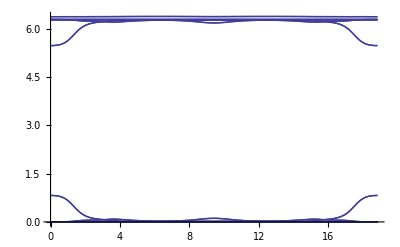

```mathematica
DiscretePlot[Piecewise[{{FCOR[T,0],T≥0&&T<Pi},{FCOR[Pi,T-Pi],T≥Pi&&T<2Pi},{FCOR[3Pi-T,Pi],T≥2Pi&&T<4Pi},{FCOR[-Pi,5Pi-T],T≥4Pi&&T≤5Pi},{FCOR[-6Pi+T,0],T≥5Pi&&T≤6Pi}}],{T,0,6Pi,Pi/50},Filling->None,Evaluate[Joined->True]]
```

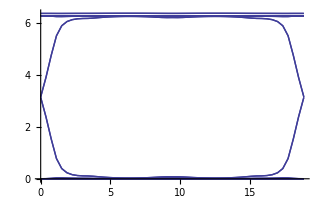

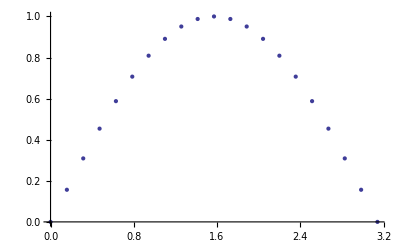

```mathematica
DiscretePlot[Sin[x],{x,0,Pi,Pi/20},Filling->None]
```

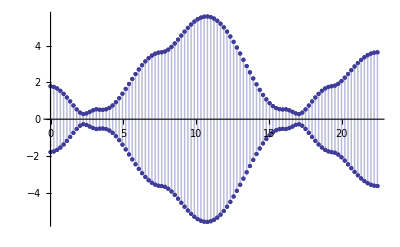

```mathematica
DiscretePlot[Piecewise[{{F[Pi-tt,0,0],tt≥0&&tt<Pi},{F[(tt-Pi)/Sqrt[2],(tt-Pi)/Sqrt[2],0],tt≥Pi&&tt<(1+Sqrt[2])Pi},{F[Pi,Pi,tt-(1+Sqrt[2])Pi],tt≥(Sqrt[2]+1)Pi&&tt<(Sqrt[2]+2)Pi},{F[Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(tt-(2+Sqrt[2])Pi)/Sqrt[3]],tt≥(2+Sqrt[2])Pi&&tt<(2+Sqrt[2]+Sqrt[3])Pi},{F[tt-(2+Sqrt[2]+Sqrt[3])Pi,0,0],tt≥(2+Sqrt[2]+Sqrt[3])Pi&&tt<(3+Sqrt[2]+Sqrt[3])Pi},{F[Pi,tt-(3+Sqrt[2]+Sqrt[3])Pi,0],tt≥(3+Sqrt[2]+Sqrt[3])Pi&&tt≤(4+Sqrt[2]+Sqrt[3])Pi}}],{tt,0,(4+Sqrt[2]+Sqrt[3])Pi,(4+Sqrt[2]+Sqrt[3])Pi/100},FillingStyle->None]
```